```mathematica
i=Input["Please input an integer value that is equal to the number of charges desired"]
```

4

```mathematica
f[i_]:=InputString[StringForm["Please write the name of charged particle number ``." ,i]];
g[i_]:=StringForm[componentNames[[i]]]∈"EFieldLine.Components.CParticle";
h[i_]:=componentNames[[i]]<>".field"-> "tparticle1.E";
```

```mathematica
j[i_]:=InputString[StringForm["Please enter the name of particle number ``.",i, "again"]]<>".q"-> Input[StringForm["Please enter the (integer) value for the charge of particle ``.",i]];
k[i_]:=InputString[StringForm["Please enter the name of particle number ``.",i, "again"]]<>".x"-> Input[StringForm["Please enter the x coordinate for the charge of particle ``.",i]];
m[i_]:=InputString[StringForm["Please enter the name of particle number ``.",i, "again"]]<>".y"-> Input[StringForm["Please enter the y coordinate for the charge of particle ``.",i]];
```

```mathematica
componentNames=Table[f[x],{x,1,i}]
```

{c1,c2,c3,c4}

StringJoin::string: String expected at position 1 in $Canceled <> ".q".

General::stop: Further output of StringJoin :: string will be suppressed during this calculation.

```mathematica
components=Table[g[x],{x,1,i}];
connections=Table[h[x],{x,1,i}]
```

{c1.field→tparticle1.E,c2.field→tparticle1.E,c3.field→tparticle1.E,c4.field→tparticle1.E}

```mathematica
Append[components,"tparticle1" ∈"EFieldLine.Components.TParticle"]
```

{c1∈EFieldLine.Components.CParticle,c2∈EFieldLine.Components.CParticle,c3∈EFieldLine.Components.CParticle,c4∈EFieldLine.Components.CParticle,tparticle1∈EFieldLine.Components.TParticle}

```mathematica
model=WSMConnectComponents["FourParticleSystem",components,connections]
```

-Graphics-

```mathematica
components={"c1"∈"EFieldLine.Components.CParticle","c2"∈"EFieldLine.Components.CParticle","c3"∈"EFieldLine.Components.CParticle","c4"∈"EFieldLine.Components.CParticle", "tparticle1" ∈ "EFieldLine.Components.TParticle"}
```

{c1∈EFieldLine.Components.CParticle,c2∈EFieldLine.Components.CParticle,c3∈EFieldLine.Components.CParticle,c4∈EFieldLine.Components.CParticle,tparticle1∈EFieldLine.Components.TParticle}

```mathematica
WSMSetValues[model,Table[j[x],{x,1,i}]]
WSMSetValues[model,Table[k[x],{x,1,i}]]
WSMSetValues[model,Table[m[x],{x,1,i}]]
```

{c1.q→1,c2.q→1,c3.q→1,c4.q→-1}

{c1.x→-1.73205,c2.x→1.73205,c3.x→0,c4.x→0}

{c1.y→-1,c2.y→-1,c3.y→2,c4.y→0}

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 12.3483"

WSMSimulate::term: Simulation of "FourParticleSystem" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "FourParticleSystem" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

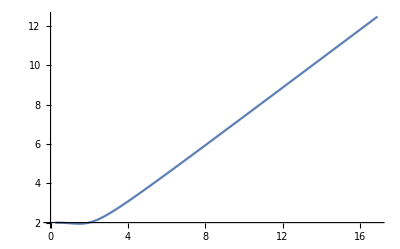
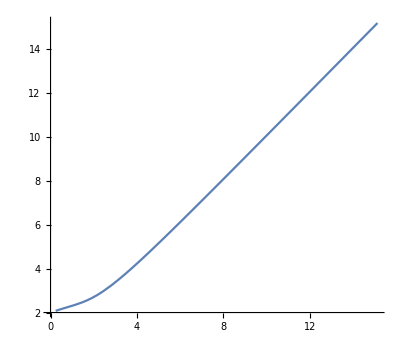
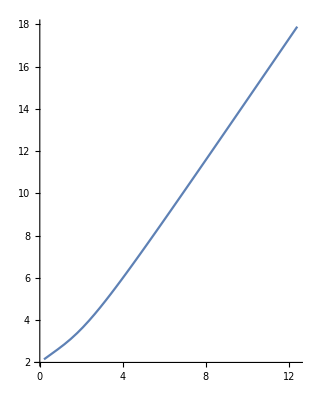
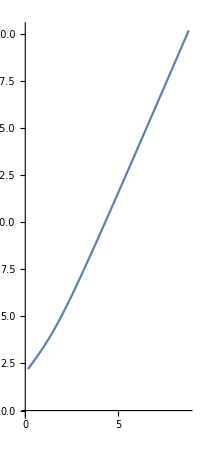
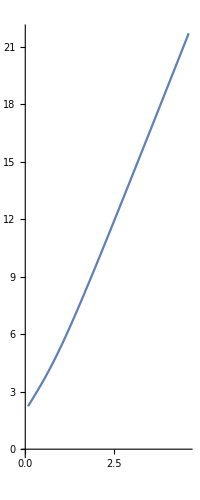
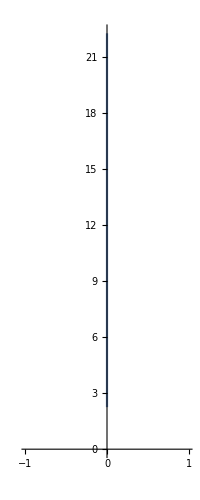
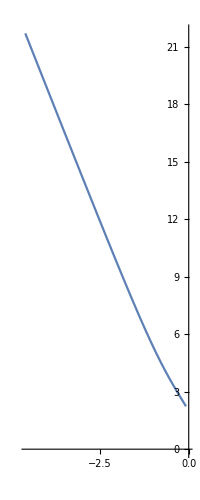
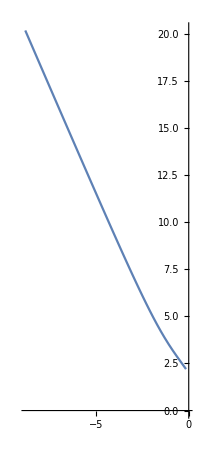
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
createStartPoints[x0_,y0_,r_,n_]:=Table[{r*Cos[theta]+x0,r*Sin[theta]+y0},{theta,0,2*Pi,2*Pi/n}];
singleEfieldLineSim[{x0_, y0_}]:= WSMSimulate["FourParticleSystem", WSMParameterValues->{"tparticle1.x0"->{x0},"tparticle1.y0"->{y0}}];
multipleEfieldLineSims[x0_,y0_,r_,n_]:=Map[singleEfieldLineSim,createStartPoints[x0,y0,r,n]];
mR1 = multipleEfieldLineSims[0,2,0.25,20];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results3=Table[EpPlot[i],{i,1,dmR1}]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 13.5731"

WSMSimulate::term: Simulation of "FourParticleSystem" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "FourParticleSystem" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

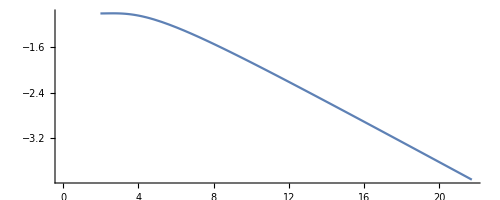
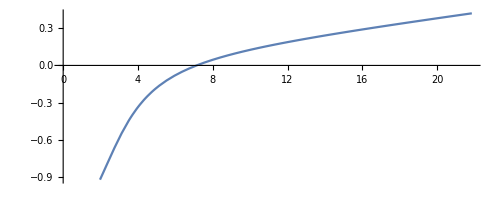
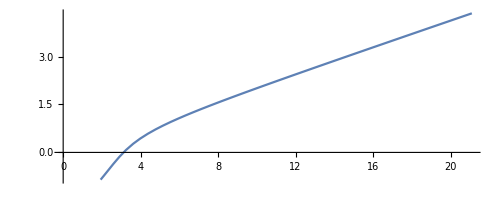
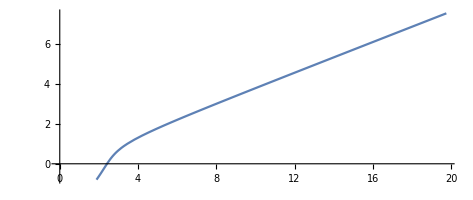
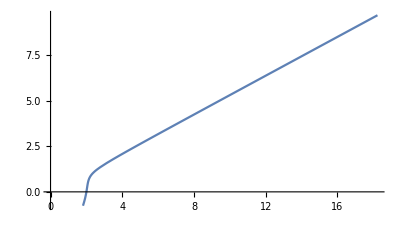
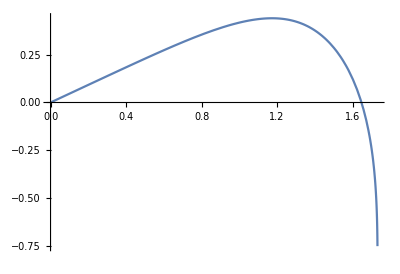
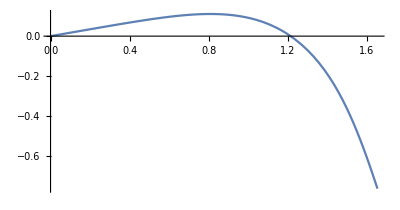
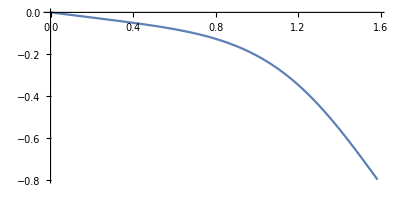
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
mR1 = multipleEfieldLineSims[1.732050807568877,-1,0.25,20];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results2=Table[EpPlot[i],{i,1,dmR1}]
```

WSMSimulate::msg: "[terminate]: came close enough"

WSMSimulate::msg: "Simulation terminated at time 9.67388"

WSMSimulate::term: Simulation of "FourParticleSystem" terminated because of a terminate statement.

WSMSimulate::msg: "[terminate]: came close enough"

General::stop: Further output of WSMSimulate :: msg will be suppressed during this calculation.

WSMSimulate::term: Simulation of "FourParticleSystem" terminated because of a terminate statement.

General::stop: Further output of WSMSimulate :: term will be suppressed during this calculation.

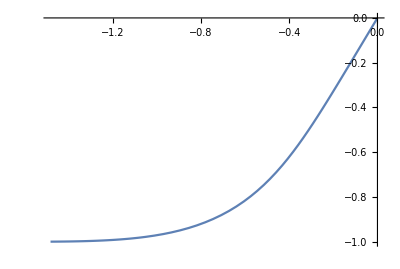
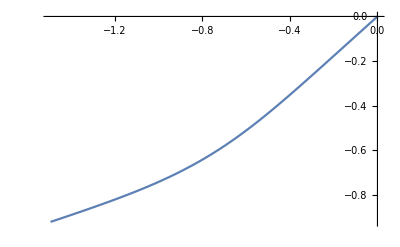
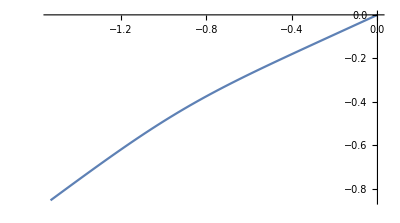
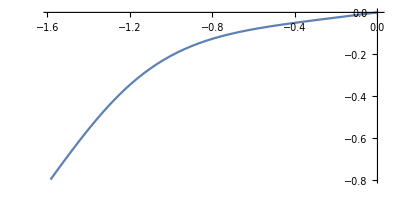
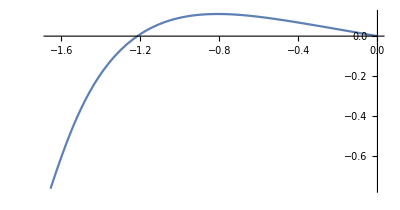
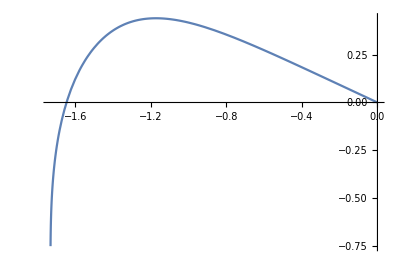
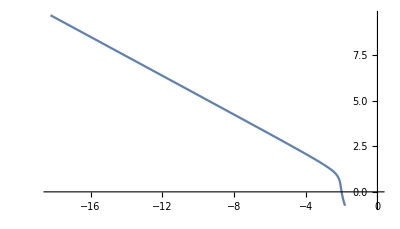
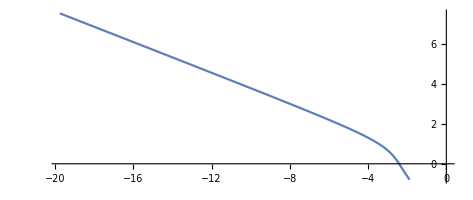
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
mR1 = multipleEfieldLineSims[-1.732050807568877,-1,0.25,20];
dmR1=Dimensions[mR1][[1]];
dmR1SimTime[i_]:=mR1[[i]]["SimulationInterval"][[2]];
yR1=Table[mR1[[i]]["tparticle1.y"],{i,1,Dimensions[mR1][[1]]}];
xR1=Table[mR1[[i]]["tparticle1.x"],{i,1,Dimensions[mR1][[1]]}];
EpPlot[i_]:=ParametricPlot[{xR1[[i]][x],yR1[[i]][x]},{x,0,dmR1SimTime[i]}];
results1=Table[EpPlot[i],{i,1,dmR1}]
```

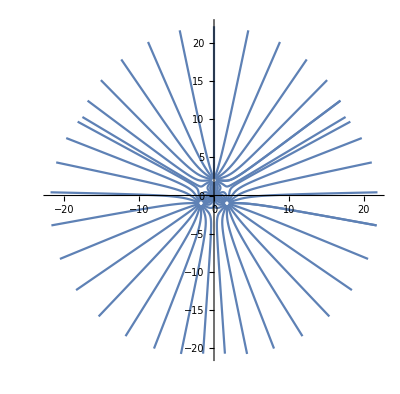

```mathematica
Show[results1,results2, results3, PlotRange-> All]
```

```mathematica
Show[%90,ImageSize->Full]
```

-Graphics-